# Proofs

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
?neurallogic`*
```

```mathematica
h[x_]:=If[x>1/2,1,0]
```

```mathematica
Margin[v_,x_List]:=Module[{μ=Mean[x],δ},
δ=μ Abs[v-1/2];
If[v>1/2,Evaluate[1/2+δ],Evaluate[v+δ]]
]
```

```mathematica
Margin2[v_,x_List]:=Module[{μ,δ},
μ=If[v>1/2,Mean[(x-1/2)/(1/2)],Mean[x/(1/2)]];
δ=μ Abs[v-1/2];
If[v>1/2,Evaluate[1/2+δ],Evaluate[v+δ]]
]
```

## NOT

```mathematica
not[w_,x_]:=1-w+(-1+2 w) x
```

```mathematica
h/@{not[1,1],not[1,0],not[0,1],not[0,0]}
```

{1,0,0,1}

```mathematica
h/@{notExp[1,1],notExp[1,0],notExp[0,1],notExp[0,0]}
```

{1,0,0,1}

```mathematica
ResourceFunction["TruthTable"][Not[Xor[w,x]],{w,x}]
```

w | x | !(w⊻x)
True | True | True
True | False | False
False | True | False
False | False | True

```mathematica
Not[Xor[w,x]]//BooleanConvert
```

(w&&x)||(!w&&!x)

```mathematica
Manipulate[Plot[not[x,y],{x,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2}}],{y,0,1}]
```

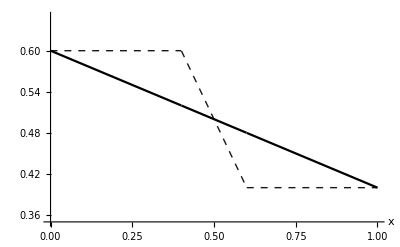

```mathematica
With[{y=0.4},Plot[{Max[Min[x,y],Min[1-x,1-y]],not[x,y]},{x,0,1},GridLines->{{1/2}},PlotRange->{{0,1},{0.35,0.65}},AxesLabel->Automatic,PlotStyle->{{Darker[Gray,0.8],Dashed,Thin},{Black}}]]
```

```mathematica
{Plot3D[Max[Min[x,y],Min[1-x,1-y]],{x,0,1},{y,0,1}],Plot3D[not[x,y],{x,0,1},{y,0,1}]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
numContours=10;
colorFunction=ColorData[{"GrayTones",{0,1}}];
```

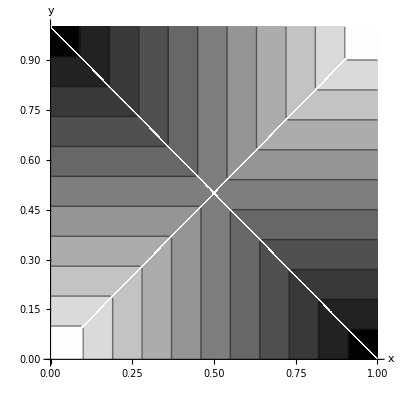
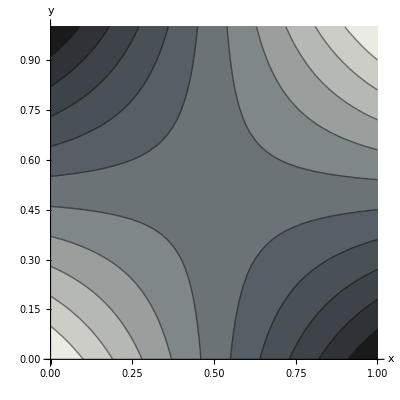
-Graphics-max(min(x, y), min(1-x, 1-y)) | -Graphics-∂NOT(x, y)

```mathematica
notp1=ContourPlot[Max[Min[x,y],Min[1-x,1-y]],{x,0,1},{y,0,1},Contours->numContours,ContourShading->Automatic,ColorFunction->GrayLevel,Frame->False,Axes->True,AxesLabel->{x,y},ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{w,x},PlotRange->All];
notp1=Labeled[notp1,Style["max(min(x, y), min(1-x, 1-y))",FontFamily->"Helvetica"]];
notp2=ContourPlot[not[x,y],{x,0,1},{y,0,1},Contours->15,ContourShading->Automatic,ColorFunction->GrayLevel,Frame->False,Axes->True,AxesLabel->{x,y},PlotLegends->BarLegend[{Automatic,{0,1}},numContours],ColorFunction->ColorData[{"GrayTones",{0,1}}],ColorFunctionScaling->False,PlotRange->All];
legend=notp2[[2,1]];
notp2=ContourPlot[not[x,y],{x,0,1},{y,0,1},Contours->numContours,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All];
notp2=Labeled[notp2,Style["∂NOT(x, y)",FontFamily->"Helvetica"]];
notPlot=Labeled[Grid[{{notp1,notp2}}],""]
```

```mathematica
legend
```

```mathematica
Export["/home/wright/coding/discrete-differentiable-networks/docs/not-plot.png",notPlot]
```

/home/wright/coding/discrete-differentiable-networks/docs/not-plot.png

## AND

```mathematica
and[x_,y_]:=Module[{m=Min[x,y]},
If[2m>1,
Evaluate[1/2+1/2(x+y)*(m-1/2)],
Evaluate[m+1/2(x+y)(1/2-m)]
]
]
```

```mathematica
{and[1,1],and[1,0],and[0,1],and[0,0]}
```

{1,1/4,1/4,0}

```mathematica
ResourceFunction["TruthTable"][And[x,y],{x,y}]
```

x | y | x&&y
True | True | True
True | False | False
False | True | False
False | False | False

## M-AND

```mathematica
(*MAnd[x_List]:=Module[{m=Min[x],μ=Mean[x],δ},
δ=μ Abs[m-1/2];
If[m>1/2,Evaluate[1/2+δ],Evaluate[m+δ]]
]*)
MAnd[x_List]:=Margin[Min[x],x]
```

```mathematica
{MAnd[{1,1}],MAnd[{1,0}],MAnd[{0,1}],MAnd[{0,0}]}
```

{1,1/4,1/4,0}

```mathematica
{MAnd[{1,1,1}],MAnd[{1,0,1}],MAnd[{0,1,1}],MAnd[{0,0,1}]}
```

{1,1/3,1/3,1/6}

```mathematica
{MAnd[{1,1,0}],MAnd[{1,0,0}],MAnd[{0,1,0}],MAnd[{0,0,0}]}
```

{1/3,1/6,1/6,0}

```mathematica
PiecewiseExpand[MAnd[{x,y}],x>0&&x<1&&y>0&&y<1]
```

Piecewise[{{1/4 (5 x-2 x^2+y-2 x y), x<1/2&&x-y≤0}, {1/4 (2-x+2 x^2-y+2 x y), x>1/2&&y>1/2&&x-y≤0}, {1/4 (3 x+2 x^2-y+2 x y), (x==1/2&&x-y≤0)||(x≥1/2&&x-y≤0&&y≤1/2)}, {1/4 (x+5 y-2 x y-2 y^2), y<1/2&&x-y>0}, {1/4 (2-x-y+2 x y+2 y^2), x>1/2&&y>1/2&&x-y>0}, {1/4 (-x+3 y+2 x y+2 y^2), True}}]

```mathematica
PiecewiseExpand[and[x,y],x>0&&x<1&&y>0&&y<1]
```

Piecewise[{{1/4 (5 x-2 x^2+y-2 x y), (x≤1/2&&x-y≤0)||(x-y≤0&&y≤1/2)}, {1/4 (2-x+2 x^2-y+2 x y), x>1/2&&y>1/2&&x-y≤0}, {1/4 (x+5 y-2 x y-2 y^2), (x≤1/2&&x-y>0)||(x-y>0&&y≤1/2)}, {1/4 (2-x-y+2 x y+2 y^2), True}}]

MAnd is identical to and in the case of two variables!

```mathematica
ForAll[{x,y},x>0&&x<1&&y>0&&y<1,MAnd[{x,y}]==and[x,y]]//Resolve
```

True

```mathematica
Manipulate[Plot[{and[x,y],MAnd[{x,y}]},{x,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2}}],{y,0,1}]
```

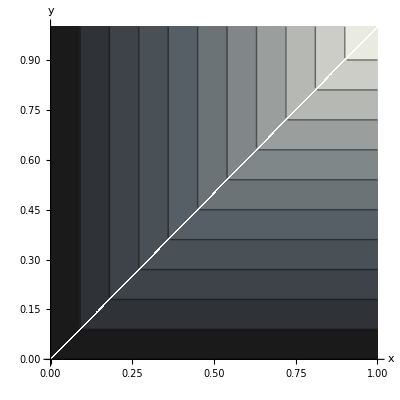
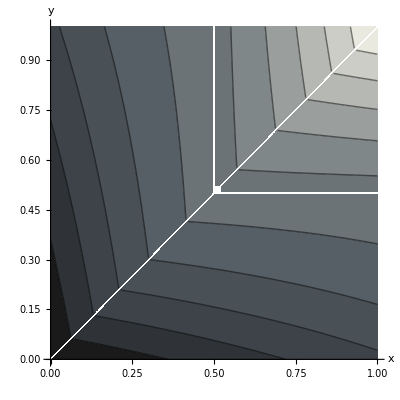
-Graphics-min(x,y) | -Graphics-∂AND(x, y)

```mathematica
andp1=ContourPlot[Min[x,y],{x,0,1},{y,0,1},Contours->numContours,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All];
andp1=Labeled[andp1,Style["min(x,y)",FontFamily->"Helvetica"]];
andp2=ContourPlot[and[x,y],{x,0,1},{y,0,1},Contours->numContours,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All];
andp2=Labeled[andp2,Style["∂AND(x, y)",FontFamily->"Helvetica"]];
andPlot=Labeled[Grid[{{andp1,andp2}}],""]
```

```mathematica
Export["/home/wright/coding/discrete-differentiable-networks/docs/and-plot.png",andPlot]
```

/home/wright/coding/discrete-differentiable-networks/docs/and-plot.png

## OR

```mathematica
or[x_,y_]:=Module[{m=Max[x,y]},
If[2m>1,
Evaluate[1/2+1/2(x+y)*(m-1/2)],
Evaluate[m+1/2(x+y)(1/2-m)]
]
]
```

```mathematica
{or[1,1],or[1,0],or[0,1],or[0,0]}
```

{1,3/4,3/4,0}

```mathematica
ResourceFunction["TruthTable"][Or[x,y],{x,y}]
```

x | y | x||y
True | True | True
True | False | True
False | True | True
False | False | False

## M-OR

```mathematica
(*MOr[x_List]:=Module[{m=Max[x],μ=Mean[x],δ},
δ=μ Abs[m-1/2];
If[m>1/2,Evaluate[1/2+δ],Evaluate[m+δ]]
]*)
MOr[x_List]:=Margin[Max[x],x]
```

```mathematica
{MOr[{1,1}],MOr[{1,0}],MOr[{0,1}],MOr[{0,0}]}
```

{1,3/4,3/4,0}

```mathematica
{MOr[{1,1,1}],MOr[{1,0,1}],MOr[{0,1,1}],MOr[{0,0,1}]}
```

{1,5/6,5/6,2/3}

```mathematica
{MOr[{1,1,0}],MOr[{1,0,0}],MOr[{0,1,0}],MOr[{0,0,0}]}
```

{5/6,2/3,2/3,0}

```mathematica
MOr[{x,y}]//PiecewiseExpand//FullSimplify
```

Piecewise[{{1/4 (x (5-2 x-2 y)+y), 2 x<1&&x≥y}, {1/4 (2-y+x (-1+2 x+2 y)), x≥y&&((2 y>1&&2 x≥1)||2 x>1)}, {1/2, (2 x==1&&x≥y)||(2 y==1&&x<y)}, {1/4 (x-2 x y+(5-2 y) y), 2 y<1&&x<y}, {1/4 (2+x (-1+2 y)+y (-1+2 y)), True}}]

```mathematica
or[x,y]//PiecewiseExpand//FullSimplify
```

Piecewise[{{1/4 (x (5-2 x-2 y)+y), 2 x≤1&&x≥y}, {1/4 (2-y+x (-1+2 x+2 y)), x≥y&&(2 x>1||2 y>1)}, {1/4 (x-2 x y+(5-2 y) y), 2 y≤1&&x<y}, {1/4 (2+x (-1+2 y)+y (-1+2 y)), True}}]

MOr is identical to or in the case of two variables!

```mathematica
Manipulate[Plot[{or[x,y],MOr[{x,y}]},{x,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2}}],{y,0,1}]
```

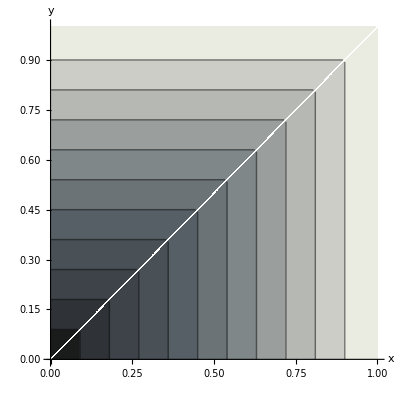
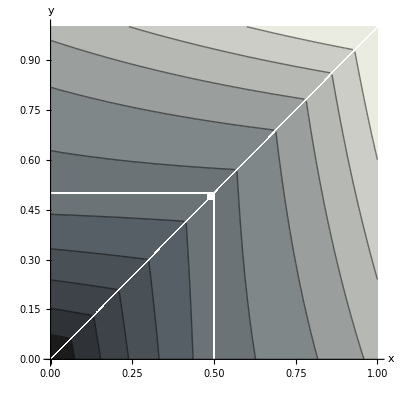
-Graphics-max(x, y) | -Graphics-∂OR(x, y)

```mathematica
orp1=ContourPlot[Max[x,y],{x,0,1},{y,0,1},Contours->numContours,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All];
orp1=Labeled[orp1,Style["max(x, y)",FontFamily->"Helvetica"]];
orp2=ContourPlot[or[x,y],{x,0,1},{y,0,1},Contours->numContours,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All];
orp2=Labeled[orp2,Style["∂OR(x, y)",FontFamily->"Helvetica"]];
orPlot=Grid[{{orp1,orp2}}]
```

## dIMPLIES

```mathematica
g[w_,x_]:=MOr[{x,1-w}]
```

```mathematica
lImplies[w_,x_]:=Min[1,1-w+x]
```

```mathematica
{g[1,1],g[1,0],g[0,1],g[0,0]}
```

{3/4,0,1,3/4}

```mathematica
ResourceFunction["TruthTable"][Implies[w,x],{w,x}]
```

w | x | w⇒x
True | True | True
True | False | False
False | True | True
False | False | True

```mathematica
ResourceFunction["TruthTable"][Or[x,Not[w]],{w,x}]
```

w | x | x||!w
True | True | True
True | False | False
False | True | True
False | False | True

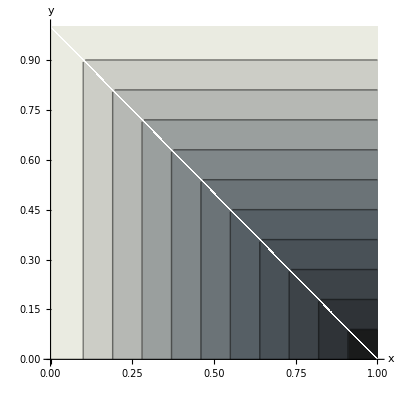
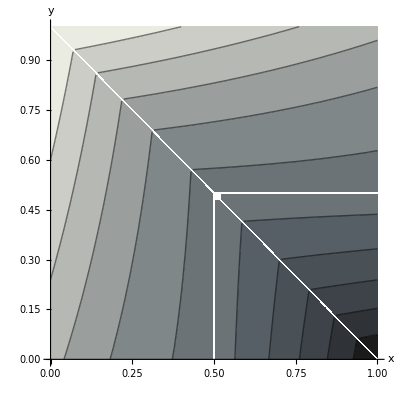
-Graphics-max(y, 1-x) | -Graphics-∂IMPLIES(x, y)

```mathematica
impp1=ContourPlot[(*lImplies[x,y]*)Max[y,1-x],{x,0,1},{y,0,1},Contours->numContours,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All];
impp1=Labeled[impp1,Style["max(y, 1-x)",FontFamily->"Helvetica"]];
impp2=ContourPlot[g[x,y],{x,0,1},{y,0,1},Contours->numContours,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All];
impp2=Labeled[impp2,Style["∂IMPLIES(x, y)",FontFamily->"Helvetica"]];
impPlot=Grid[{{impp1,impp2}}]
```

```mathematica
logicGates=Grid[{{Grid[{{legend}}],Grid[{Style[#,16,FontFamily->"Helvetica"]&/@{"¬(x⊕y)","x∧y","x∨y","x⇒y"},{notp1,andp1,orp1,impp1},{notp2,andp2,orp2,impp2}},Dividers->{{LightGray,LightGray,LightGray,LightGray,LightGray},{False,LightGray}}]}}]
```

| ¬(x⊕y) | x∧y | x∨y | x⇒y
-Graphics-max(min(x, y), min(1-x, 1-y)) | -Graphics-min(x,y) | -Graphics-max(x, y) | -Graphics-max(y, 1-x)
-Graphics-∂NOT(x, y) | -Graphics-∂AND(x, y) | -Graphics-∂OR(x, y) | -Graphics-∂IMPLIES(x, y)

```mathematica
Export["/home/wright/coding/discrete-differentiable-networks/docs/logic-gates.png",logicGates]
```

/home/wright/coding/discrete-differentiable-networks/docs/logic-gates.png

```mathematica
PiecewiseExpand/@{Max[y,1-x],Min[1,1-x+y]}
```

{Piecewise[{{1-x, x+y≤1}, {y, True}}],Piecewise[{{1, x-y≤0}, {1-x+y, True}}]}

```mathematica
{Max[y,1-x],Min[1,1-x+y]}/.{x->0.1,y->0.3}
```

{0.9,1}

## dMAJORITY

```mathematica
MajorityIndex[x_List]:=Quotient[Length[x]-1,2]
```

```mathematica
MajorityIndex[x_List]:=Floor[(Length[x]-1)/2]
```

```mathematica
MajorityIndex/@{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}
```

{0,0,1,1,2,2}

```mathematica
MajorityBit[x_List]:=Take[Sort[x],{MajorityIndex[x]+1}][[1]]
```

```mathematica
MajorityBit/@{{1},{2,1},{1,3,2},{2,1,4,3},{1,2,3,4,5},{6,3,2,4,5,1},{7,6,5,4,3,2,1}}
```

{1,1,2,2,3,3,4}

```mathematica
(*DMajority[x_List]:=Module[{mbit=MajorityBit[x],margin,mean,marginDelta},
margin=Abs[mbit-1/2];
mean=Mean[x];
marginDelta=mean*margin;
If[mbit>1/2,
Evaluate[1/2+marginDelta],
Evaluate[mbit+marginDelta]]
]*)
```

```mathematica
DMajority[x_List]:=Margin[MajorityBit[x],x]
```

```mathematica
DMajority[{0.1,0.2,0.8,0.9,0.52}]
```

0.51008

```mathematica
DMajority[{0.1,0.55,0.8,0.9,0.52}]
```

0.5287

```mathematica
DMajority[{x1,x2,x3,x4,x5}]
```

If[x3>1/2,1/2+1/5 (x1+x2+x3+x4+x5) Abs[-1/2+x3],x3+1/5 (x1+x2+x3+x4+x5) Abs[-1/2+x3]]

```mathematica
Majority[x,y,z]//BooleanConvert
```

(x&&y)||(x&&z)||(y&&z)

```mathematica
Majority[x1,x2,x3,x4,x5,x6]//BooleanConvert
```

(x1&&x2&&x3&&x4)||(x1&&x2&&x3&&x5)||(x1&&x2&&x3&&x6)||(x1&&x2&&x4&&x5)||(x1&&x2&&x4&&x6)||(x1&&x2&&x5&&x6)||(x1&&x3&&x4&&x5)||(x1&&x3&&x4&&x6)||(x1&&x3&&x5&&x6)||(x1&&x4&&x5&&x6)||(x2&&x3&&x4&&x5)||(x2&&x3&&x4&&x6)||(x2&&x3&&x5&&x6)||(x2&&x4&&x5&&x6)||(x3&&x4&&x5&&x6)

```mathematica
bmaj[x_,y_,z_]:=Min[Max[x,y],Max[x,z],Max[y,z]]
```

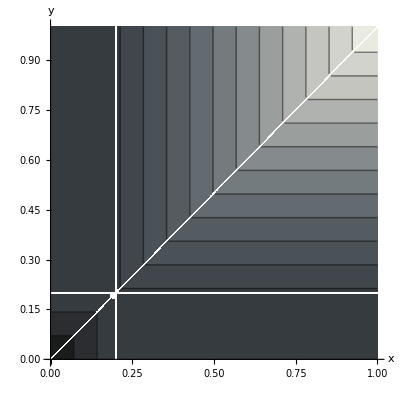
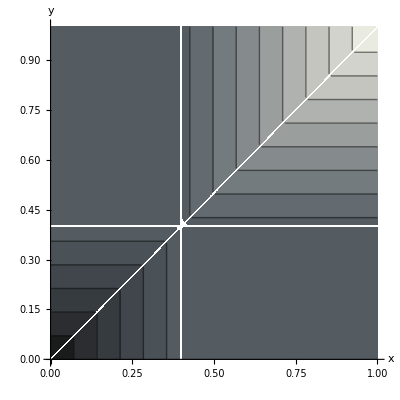
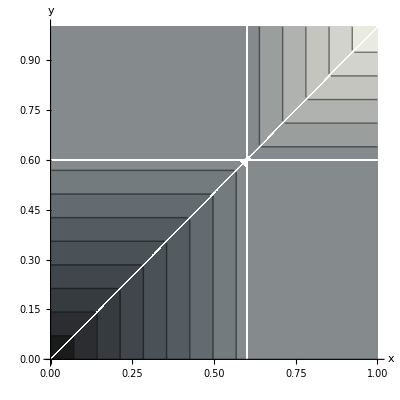
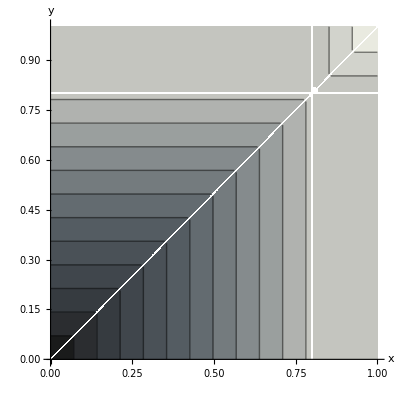

```mathematica
majp1=Map[ContourPlot[bmaj[x,y,#],{x,0,1},{y,0,1},Contours->numContours+3,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All]&,{0.2,0.4,0.6,0.8}]
```

```mathematica
legend
```

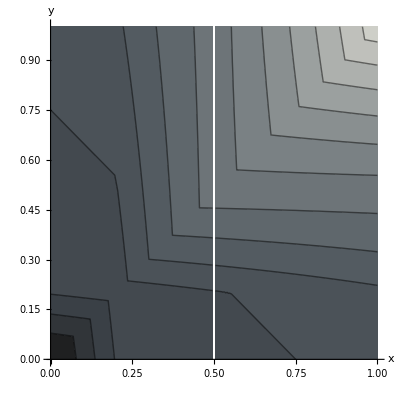
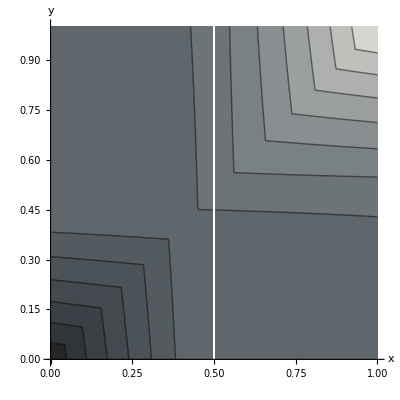
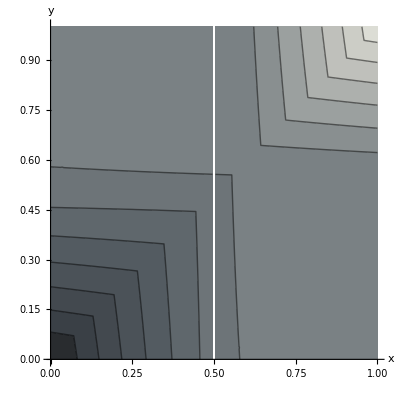
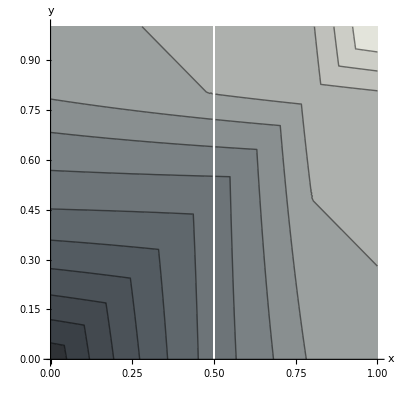

```mathematica
majp2=Map[ContourPlot[DMajority[{x,y,#}],{x,0,1},{y,0,1},Contours->numContours+3 ,ContourShading->Automatic,ColorFunction->colorFunction,ColorFunctionScaling->False,Frame->False,Axes->True,AxesLabel->{x,y},PlotRange->All]&,{0.2,0.4,0.6,0.8}]
```

```mathematica
majorityGates=Grid[{{Grid[{{legend}}],Grid[{Style[#,16,FontFamily->"Helvetica"]&/@{"z=0.2","z=0.4","z=0.6","z=0.8"},majp1,Style["min(max(x,y), max(x,z), max(y,z))",11,FontFamily->"Helvetica"]&/@{1,2,3,4},majp2,Style["∂MAJORITY(x, y, z)",11,FontFamily->"Helvetica"]&/@{1,2,3,4}},Dividers->{{LightGray,LightGray,LightGray,LightGray,LightGray},{False,LightGray}}]}}]
```

| z=0.2 | z=0.4 | z=0.6 | z=0.8
-Graphics- | -Graphics- | -Graphics- | -Graphics-
min(max(x,y), max(x,z), max(y,z)) | min(max(x,y), max(x,z), max(y,z)) | min(max(x,y), max(x,z), max(y,z)) | min(max(x,y), max(x,z), max(y,z))
-Graphics- | -Graphics- | -Graphics- | -Graphics-
∂MAJORITY(x, y, z) | ∂MAJORITY(x, y, z) | ∂MAJORITY(x, y, z) | ∂MAJORITY(x, y, z)

```mathematica
Export["/home/wright/coding/discrete-differentiable-networks/docs/majority-gates.png",majorityGates]
```

/home/wright/coding/discrete-differentiable-networks/docs/majority-gates.png

## dCOUNT

```mathematica
BooleanCountingFunction[{2},{x1,x2,x3}]
```

(x1&&x2&&!x3)||(x1&&!x2&&x3)||(!x1&&x2&&x3)

## margin trick

```mathematica
Manipulate[
Block[{m,eps,thresholdLine,marginLine,representativeLine,augmentation},
m=Min[x,y];
eps=0.001;
augmentation=Mean[{x,y}]Abs[m-1/2];
thresholdLine=Line[{{1/2,-1},{1/2,1}}];
marginLine={Line[{{m,0.2},{1/2,0.2}}],Text[Style["margin",Bold,FontFamily->"Helvetica"],{m+(1/2-m)/2,0.3}]};
representativeLine={Line[{{m,-0.8},{m,1}}],Text[Style["representative bit",Bold,FontFamily->"Helvetica"],{m,-0.9}]};
Labeled[Plot[
{
Callout[If[m<=1/2,
If[x>=(m+augmentation-eps)&&x<=(m+augmentation+eps),1,Nothing],
If[x>=(1/2+augmentation-eps)&&x<=(1/2+augmentation+eps),1,Nothing]
],Style["augmented bit",Bold,FontColor->Darker[Green]],{If[m>1/2,1/2+augmentation/2,m+augmentation/2],1.2},CalloutStyle->{Darker[Green]},Background->Transparent],
If[m<=1/2,
If[x>m && x<=(m+augmentation),1,Nothing],
If[x>1/2&&x<(1/2+augmentation),1,Nothing]
]
},
{x,0,1},
PlotRange->{{If[m>1/2,0.4,0],If[m>1/2,1,0.6]},{-1,1}},
PlotStyle->Transparent,
Filling->{1->1,2->-0.8},
FillingStyle->Lighter[Green,0.8],
Axes->{True,False},
Ticks->{True,False},
Epilog->{Directive[Black],representativeLine,Directive[Gray,Dashed],thresholdLine,marginLine},
ImagePadding->{{0,0},{0,25}}
],If[m>1/2,Style["high margin",FontFamily->"Helvetica"],Style["low margin",FontFamily->"Helvetica"]],Bottom]
],{x,0,1},{y,0,1}
]
```

```mathematica
(* x= 0.906, y=0.226 *)
```

```mathematica
g1=-Graphics-
```

-Graphics-

```mathematica
(* x = 0.906, y = 0.826 *)
```

```mathematica
g2=-Graphics-
```

-Graphics-

```mathematica
g3=GraphicsRow[{g1,g2},Dividers->{{False,LightGray,False}}]
```

-Graphics-

```mathematica
Export["/home/wright/coding/discrete-differentiable-networks/docs/margin-trick.png",g3]
```

/home/wright/coding/discrete-differentiable-networks/docs/margin-trick.png